```mathematica
(* Verified *)
CW[n_] := {{0, 0, 0,1, 0, 0}, {0, 0, 0,0,1, 0}, {0, 0, 0, 0 ,0, 1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0, 0}, {0, 0, -n^2, 0, 0,0}} ;
```

```mathematica
cmat[ab_, tau_, tf_] := MatrixExp[-(tau - tf) ab // Transpose][[4;;6, 1;;3]];
```

```mathematica
cmat[CW[5], 0.1, 1]  // MatrixForm
```

```mathematica
(*(100 (cmat[CW[5], 0.1, 1] // Transpose).cmat[CW[5], 0.1, 1])// MatrixForm*)


 (*100 (cmat[CW[5], 0.1, 1][[4;;6, 1;;3]] // Transpose).cmat[CW[5], 0.1, 1][[4;;6, 1;;3]].{0,0,1}*)

(*(deltaT.(cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta // Sqrt) /. {A -> CW[5], tf -> 1, delta -> {0,0,1}, Tmax -> 100, deltaT -> {{0,0,1}}, tau -> 0.1})[[1]]*)


100 (cmat[CW[5], 0.1, 1] // Transpose).cmat[CW[5], 0.1, 1].{0,0,1} / (({{0,0,1}}.(cmat[CW[5], 0.1, 1] // Transpose).cmat[CW[5], 0.1, 1].{0,0,1} // Sqrt)[[1]]);
```

```mathematica
xrf[tf_, delta_, h_, deltaT_, A_, n_, Rr_] := NIntegrate[  h n^2 Rr (cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta / (deltaT.(cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta // Sqrt)[[1]]  ,{tau, 0, tf}];
```

```mathematica
x3fanalytical[tf_, h_, n_]:= h(2Floor[n tf / Pi]+1+ Mod[Floor[n tf / Pi], 2] Cos[n tf] - (Mod[Floor[n tf / Pi], 2] - 1)(- Cos[n tf]));
```

```mathematica
x3fanalytical[1,  100, 5] // N
```

```mathematica
xrf[1, {0, 0, 1}, 100, {{0,0,1}}, CW[5],5, 1] 
f[1, {0, 0, 1}, 100, {{0,0,1}}, CW[5],5, 1]
```

```mathematica
(* NSolve[x3fanalytical[t1, 100, 5] == 0, t1];
```

```mathematica
ContourPlot[x3fanalytical[t1, h1, 5] == 0, {t1, 0, 10}, {h1, 0, 100}];
```

```mathematica
Graphics3D[Point[SpherePoints[200]]];

columntorow[x_] := {x}
```

```mathematica
points = SpherePoints[1000];
points[[1]];
tfs = ConstantArray[1, 1000];
tfs[[1]];
hs = ConstantArray[100, 1000];
hs[[1]];
As = ConstantArray[CW[5], 1000];
As[[1]] // MatrixForm;
ns = ConstantArray[5, 1000];
ns[[1]];
Rrs = ConstantArray[1, 1000];
Rrs[[1]];
pointsT = columntorow /@ points;
pointsT[[1]] // MatrixForm;
(*{tfs, points, hs, pointsT, As, ns, Rrs}*)

rd = MapThread[xrf, {tfs, points, hs, pointsT, As, ns, Rrs}];
(*
Thread[f[tfs, points, hs, pointsT, As, ns, Rrs]];
in = {tfs, points, hs, pointsT, As, ns, Rrs} // Transpose;
xrf /@ in; *)
```

```mathematica
rdpoints = Map[Re, rd, {2}];
```

```mathematica
Graphics3D[Point[rdpoints]];
```

```mathematica
first2[x_] := {x[[1]], x[[2]]}
```

```mathematica
d2 = Map[first2, rdpoints];
Graphics[Point[d2]]
```

```mathematica
ConvexHullRegion[d2]
rdboundary = PolygonCoordinates[ConvexHullRegion[d2]];
```

```mathematica
Show[%1314,Axes->True]
```

```mathematica
Region[ConvexHullRegion[d2],Epilog->{Black,Point[d2]}]
```

```mathematica
(* Outputs min, max ratios between the reachable sets as well as the angles at which they occur
*)
reachablestatistics[ps_, a_] := 0;
```

```mathematica
Clear[rdboundarythetas];
```

```mathematica
rdboundarythetas[p_] := MapThread[VectorAngle, {ConstantArray[{1,0 }, p // Length], p}];
ell[theta_, a_]:= (a // Inverse).{Cos[theta], Sin[theta]};
```

```mathematica
vectors[thetas_, a_] := MapThread[ell, {thetas, ConstantArray[a, thetas // Length]}];
mmratios[v1s_, v2s_] := {Max[(Norm /@ v1s) / (Norm /@ v2s)], Min[(Norm /@ v1s) / (Norm /@ v2s)]};
mmangles[v1s_, v2s_, thetas_] := {thetas[[Position[(Norm /@ v1s) / (Norm /@ v2s), Max[(Norm /@ v1s) / (Norm /@ v2s)]][[1]]]], thetas[[Position[(Norm /@ v1s) / (Norm /@ v2s), Min[(Norm /@ v1s) / (Norm /@ v2s)]][[1]]]]}
```

{1.18012×10^-6,2.48356×10^-7}

{{0.155195},{1.85073}}

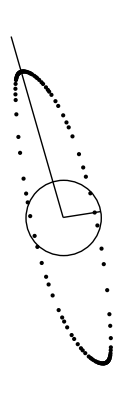

```mathematica
tdata = rdboundarythetas[rdboundary];
circularvecs = vectors[tdata, {{1000, 0}, {0, 1000}}];
rats = mmratios[circularvecs, rdboundary]
ans = mmangles[circularvecs, rdboundary, tdata]




Show[{Graphics[Point[rdboundary]], Graphics[Circle[{0, 0}, 1000]], Graphics[Line[1000 AnglePath[{ans[[1, 1]]}]]], Graphics[Line[5000AnglePath[{ans[[2, 1]]}]]]}]
```